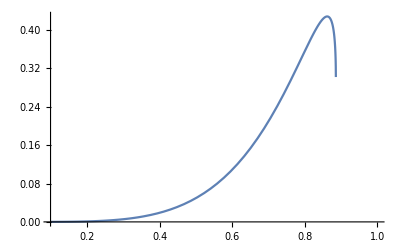

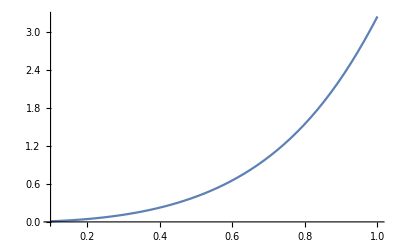

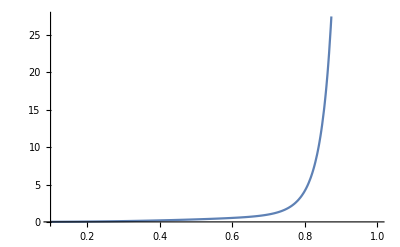

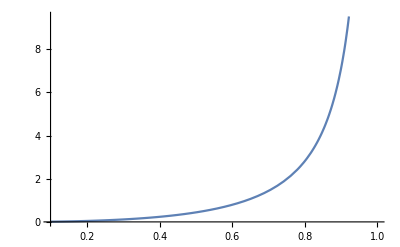

```mathematica
M   = 0.1349764 ;
m           = 0.93827231 ;
s[Q2_,x_]:=Q2*(1/x-1)+m^2;
W[Q2_,x_]:=Sqrt[s[Q2,x]];
E1CM[Q2_,x_]:=(W[Q2,x]^2+Q2+m^2)/(2*W[Q2,x]);
E3CM[Q2_,x_]:=(W[Q2,x]^2-M^2+m^2)/(2*W[Q2,x]);
P1CM[Q2_,x_]:= Sqrt[E1CM[Q2,x]^2-m^2];
P3CM[Q2_,x_]:= Sqrt[E3CM[Q2,x]^2-m^2];
y[Q2_,x_,E_]:=Q2/(2*m*x*E);
Λ[m12_,m22_,m32_]:= m12^2+m22^2+m32^2-2*m12*m22-2*m12*m32-2*m22*m32;
tmin[Q2_,x_]:=-((Q2+M^2)^2/4/W[Q2,x]^2-(P1CM[Q2,x]-P3CM[Q2,x])^2);
tmin0[Q2_,x_]:=1/(2 s[Q2,x])(s[Q2,x]^2-s[Q2,x](-Q2+2 m^2+M^2)+(Q2+m^2)(m^2-M^2)-Sqrt[Λ[s[Q2,x],-Q2,m^2]Λ[s[Q2,x],M^2,m^2]]);
γ2[Q2_,x_]:=4m ^2x^2/Q2;
a[Q2_,x_]:=Sqrt[1-M^2/Q2*(2x(1-x)+γ2[Q2,x])/(1-x)^2+M^4/Q2^2*x^2/(1-x)^2];
tmin1[Q2_,x_]:=Q2*(2(1-x)(1-Sqrt[1+γ2[Q2,x]]a[Q2,x])+γ2[Q2,x]-(2x+γ2[Q2,x])M^2/Q2)/(4x(1-x)+γ2[Q2,x]);
tmin2[Q2_,x_]:=m^2/s[Q2,x]^2(Q2+M^2)^2(1-(Q2-2 m^2-M^2)/s[Q2,x]);
tmin3[Q2_,x_]:=γ2[Q2,x]Q2/(4(1-x))(1-(γ2[Q2,x]/4-M^2/Q2)(2-x)/(1-x)+1/(4(1-x)^2)(γ2[Q2,x](γ2[Q2,x]/4-M^2/Q2)(2-2 x+x^2+γ2[Q2,x]^2/4(3-x)(1-x)+4M^4/Q2^2)));
tmin4[Q2_,x_]:=m^2x^2/(1-x);
tminji[ξ_]:=4m^2ξ^2/(1-ξ);


QQ2=2.1;

Plot[{tmin2[QQ2,x]-tmin1[QQ2,x]},{x,0.1,1.}]
Plot[{tmin2[QQ2,x]},{x,0.1,1.}]
Plot[{tmin3[QQ2,x]},{x,0.1,1.}]
Plot[{tmin4[QQ2,x]},{x,0.1,1.}]
```

```mathematica
tmin0[2.21,0.1]
m
M
```

0.000381281

0.134976

0.938272